# Numerical Solution - Gas Electron Multiplier

- Potential

```mathematica
ngasdata= Import["/home/2317101h/year_3/group_project/numerical_sol/section2.2/electricField.dat"];
ngasreshape = ArrayReshape[ngasdata, {100,100}];
```

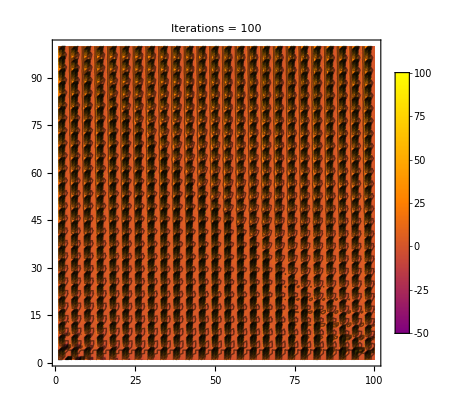

```mathematica
epilog=ListContourPlot[ngasreshape,ContourShading->None, Contours->Function[{min,max},Range[min,max,10]]][[1]];
s=ListDensityPlot[ngasreshape,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->epilog,PlotLabel->"Iterations = 100"]
```

- Create a GIF (Potential)

```mathematica
Do[Export["/home/2317101h/year_3/group_project/numerical_sol/section2.2/anim/pics/"<>ToString[i]<>".png",ListDensityPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.2/anim/" <> ToString[i] <> ".dat"],{100,100}],PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->ListContourPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.2/anim/" <> ToString[i] <> ".dat"], {100,100}],ContourShading->None, Contours->Function[{min,max},Range[min,max,10]]][[1]],PlotLabel->"Iterations =" <>ToString[i] ]],{i, 0, 9900, 100}]
```